```mathematica
Quit[]
```

## Practical CP1 - 1 Exercise 1-1

```mathematica
f= 4x^2 +4x+1
df=D[f,{x,1}]
```

1+4 x+4 x^2

4+8 x

```mathematica
g=(2x+1)^2
dg=D[g,{x,1}]
```

(1+2 x)^2

```mathematica
4 (1+2 x)
```

```mathematica
c = e^(2x+1)
dc = D[c,{x,1}]
```

e^(1+2 x)

2 e^(1+2 x) Log[e]

```mathematica
h = ln(2x+1)
dh = D[h,{x,1}]
```

ln (1+2 x)

2 ln

```mathematica
p = (2x+1)^0.5
dp = D[p,{x,1}]
```

(1+2 x)^0.5

1./(1+2 x)^0.5

```mathematica
l = (2x+1)^(-1)
dl = D[l,{x,1}]
```

1/(1+2 x)

-2/(1+2 x)^2

```mathematica
z=x+3;
```

```mathematica
z
```

3+x

## Exercise 1-2

```mathematica
Quit[]
```

```mathematica
a = Sin[t]^2+ Cos[t]^2
da = D[a, {t,1}]
```

Cos[t]^2+Sin[t]^2

0

```mathematica
b = Sin[t^2]+Cos[t^2]
db = D[b,{t,1}]
```

Cos[t^2]+Sin[t^2]

2 t Cos[t^2]-2 t Sin[t^2]

```mathematica
c = (Sin[t]+Cos[t])^2
dc = D[c,{t,1}]
```

(Cos[t]+Sin[t])^2

2 (Cos[t]-Sin[t]) (Cos[t]+Sin[t])

```mathematica
d = Sin[t] * Cos[t]
dd = D[d,{t,1}]
```

Cos[t] Sin[t]

Cos[t]^2-Sin[t]^2

```mathematica
g = (Cos[t]^2)^(1/2)
dg = D[g,{t,1}]
```

√(Cos[t]^2)

-(Cos[t] Sin[t])/(√(Cos[t]^2))

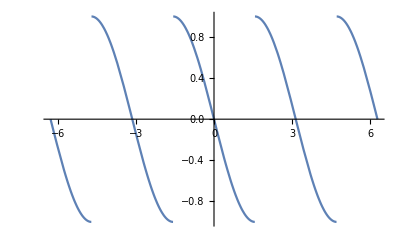

```mathematica
Plot[dg, {t,-2 Pi, 2 Pi}]
```

```mathematica
f = Cos[t]/Sin[t]
df = D[f,{t,1}]
```

Cot[t]

-Csc[t]^2

## Exercise 1-3

```mathematica
Quit[]
```

```mathematica
a = x^2
da = D[a,{x,1}]
```

x^2

2 x

```mathematica
b = 2^x
db = D[b,{x,1}]
```

2^x

2^x Log[2]

```mathematica
c = (s-1)^(2s)
dc = D[c,{s,1}]
```

(-1+s)^(2 s)

(-1+s)^(2 s) ((2 s)/(-1+s)+2 Log[-1+s])

## Exercise 1-4

```mathematica
Quit[]
```

```mathematica
f = Log[2x+1]
```

Log[1+2 x]

```mathematica
Series[f,{x,0,1}]
```

2 x+O[x]^2

```mathematica
Series[f,{x,0,2}]
```

2 x-2 x^2+O[x]^3

```mathematica
Series[f,{x,0,3}]
```

2 x-2 x^2+(8 x^3)/3+O[x]^4

## Exercise 1-5

```mathematica
Quit[]
```

```mathematica
f = x/Tan[x]
```

x Cot[x]

```mathematica
Limit[f,x-> 0]
```

1

```mathematica
b=(x^2-1)/Log[x]
```

(-1+x^2)/Log[x]

```mathematica
Limit[b,x->1]
```

2

```mathematica
c=(x^3-x^2-x+1)/(x^2-2x+1)
```

(1-x-x^2+x^3)/(1-2 x+x^2)

```mathematica
Limit[c,x->1]
```

2

```mathematica
d = (Sin[x]-x)/(Cos[x]-1)
```

(-x+Sin[x])/(-1+Cos[x])

```mathematica
Limit[d, x-> 0]
```

0